```mathematica
f1[x_,y_]:=2x*x-x y-y*y+2x-2y+6;
f2[x_,y_]:=y-0.5x*x-1;
```

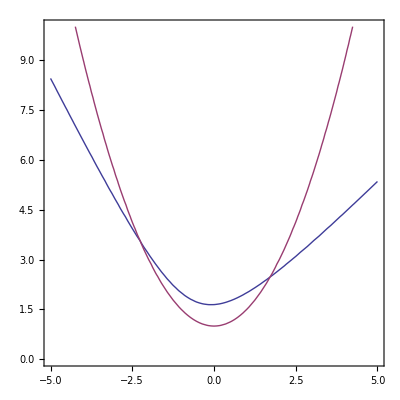

```mathematica
ContourPlot[{f1[x,y],f2[x,y]},{x,-5,5},{y,0,10}]
```

```mathematica
x0=2; y0=2;
```

```mathematica
Phi1[x_,y_]:=x+a f1[x,y]+b f2[x,y];
Phi2[x_,y_]:=y+c f1[x,y]+ d f2[x,y];
```

```mathematica
ab=Solve[(D[Phi1[x,y],x]/.{x->x0,y->y0})==0 && (D[Phi1[x,y],y]/.{x->x0,y->y0})==0,{a,b}]//Flatten
```

{a→0.125,b→1.}

```mathematica
cd=Solve[(D[Phi2[x,y],x]/.{x->x0,y->y0})==0 && (D[Phi2[x,y],y]/.{x->x0,y->y0})==0,{c,d}]//Flatten
```

{c→0.25,d→1.}

```mathematica
xn[0]:=x0;
yn[0]:=y0;
xn[k_]:=(Phi1[xn[k-1],yn[k-1]]/.ab);
yn[k_]:=(Phi2[xn[k-1],yn[k-1]]/.cd);
```

```mathematica
n=1;
Eps=1/2 10^-4;
While[Max[Abs[xn[n]-xn[n-1]],Abs[yn[n]-yn[n-1]]]>Eps,Print[{xn[n-1],yn[n-1]}];n++]
n-1
f1[xn[#],yn[#]]&[n-1]
f2[xn[#],yn[#]]&[n-1]
```

{2,2}

{1.75,2.5}

{1.71875,2.46875}

{1.71924,2.47803}

{1.71851,2.47643}

{1.71858,2.47678}

6

0.0000845616

-6.71118×10^-6

```mathematica
x0=-2; y0=4;
```

```mathematica
Phi1[x_,y_]:=x+a f1[x,y]+b f2[x,y];
Phi2[x_,y_]:=y+c f1[x,y]+ d f2[x,y];
```

```mathematica
ab=Solve[(D[Phi1[x,y],x]/.{x->x0,y->y0})==0 && (D[Phi1[x,y],y]/.{x->x0,y->y0})==0,{a,b}]//Flatten
```

{a→-0.166667,b→-1.33333}

```mathematica
cd=Solve[(D[Phi2[x,y],x]/.{x->x0,y->y0})==0 && (D[Phi2[x,y],y]/.{x->x0,y->y0})==0,{c,d}]//Flatten
```

{c→0.333333,d→1.66667}

```mathematica
xn[0]:=x0;
yn[0]:=y0;
xn[k_]:=(Phi1[xn[k-1],yn[k-1]]/.ab);
yn[k_]:=(Phi2[xn[k-1],yn[k-1]]/.cd);
```

```mathematica
n=1;
Eps=1/2 10^-4;
While[Max[Abs[xn[n]-xn[n-1]],Abs[yn[n]-yn[n-1]]]>Eps,Print[{xn[n-1],yn[n-1]}];n++]
n-1
f1[xn[#],yn[#]]&[n-1]
f2[xn[#],yn[#]]&[n-1]
```

{-2,4}

{-2.33333,3.66667}

{-2.25926,3.57407}

{-2.26229,3.55818}

{-2.25855,3.55151}

{-2.2582,3.54982}

{-2.25796,3.54926}

{-2.25791,3.54909}

8

-0.000069924

4.86921×10^-6